```mathematica
SimpSymbol[symbol_]:=λ^StringCount[SymbolName[symbol],"x"]
```

```mathematica
SimpSymbol[n134x25]
```

λ

```mathematica
simpRep=Table[k->SimpSymbol[k],{k,realyNullAtomVars}];Take[simpRep,3]
```

{n1x2x3x4x5→λ^4,n1x2x3x45→λ^3,n1x2x35x4→λ^3}

```mathematica
Total[Table[allGraphs[k,"colofourrealnull"],{k,{quad1Key}}]]+Total[Table[allGraphs[k,"colofourrealnull"],{k,{alfa1Key}}]]//Simplify
```

-4 n12345+n1234x5+2 n1235x4+n123x45-n123x4x5+2 n1345x2+n134x25-n134x2x5-n135x2x4+n13x245-n13x25x4-n13x2x45+n13x2x4x5

```mathematica
Total[Table[allGraphs[k,"colofourrealnull"],{k,{quad1Key}}]]
```

-6 n12345+2 n1234x5+2 n1235x4+n123x45-n123x4x5+2 n1345x2+n134x25-n134x2x5+n135x24-n135x2x4+2 n13x245-n13x24x5-n13x25x4-n13x2x45+n13x2x4x5

```mathematica
Total[Table[allGraphs[k,"colofourrealnull"],{k,{alfa1Key}}]]
```

2 n12345-n1234x5-n135x24-n13x245+n13x24x5

```mathematica
-Total[Table[allGraphs[k,"colofourrealnull"],{k,{alfa1Key}}]]
```

-2 n12345+n1234x5+n135x24+n13x245-n13x24x5

```mathematica
Total[Table[allGraphs[k,"colofourrealnull"],{k,{alfa1Key,beta1Key,gamma1Key,delta1Key,epsilon1Key}}]]/.simpRep
```

10-15 λ+5 λ^2

```mathematica
ChromaticPolynomial[allGraphs[alfa1Key,"graph"],x]
```

2 x-3 x^2+x^3

```mathematica
(-6+11 λ-6 λ^2+λ^3)-(10-15 λ+5 λ^2)
```

```mathematica
-16+26 λ-11 λ^2+λ^3/.λ->4
```

-24

```mathematica
10-15 λ+5 λ^2/.λ->4
```

30

```mathematica
GraphEndsIn[g_,v_]:=Block[{result,list},
list=Select[IncidenceList[g,v],#[[2]]==v&];
result=list;
Table[
If[couple[[2]]==v,
result=Join[result,GraphEndsIn[g,couple[[1]]]]
]
,
{couple,list}
];
DeleteDuplicates[result]
]
```

```mathematica
styles=Association[];
```

```mathematica
hl=Table[styles[sym]=Green,{sym,Flatten[DeleteDuplicates[Table[ListofVars[allGraphs[k,"colofourrealnull"]],{k,{alfa1Key}}]]]}]
```

{RGBColor[0, 1, 0],RGBColor[0, 1, 0],RGBColor[0, 1, 0],RGBColor[0, 1, 0],RGBColor[0, 1, 0]}

```mathematica
styles
```

<|n13x24x5→RGBColor[0, 1, 0],n12345→RGBColor[0, 1, 0],n1234x5→RGBColor[0, 1, 0],n135x24→RGBColor[0, 1, 0],n13x245→RGBColor[0, 1, 0],n14x25x3→RGBColor[0, 1, 0],n1245x3→RGBColor[0, 1, 0],n134x25→RGBColor[0, 1, 0],n14x235→RGBColor[0, 1, 0],n1x24x35→RGBColor[0, 1, 0],n124x35→RGBColor[0, 1, 0],n1x2345→RGBColor[0, 1, 0],n13x25x4→RGBColor[0, 1, 0],n1235x4→RGBColor[0, 1, 0],n14x2x35→RGBColor[0, 1, 0],n1345x2→RGBColor[0, 1, 0]|>

```mathematica
Table[styles[sym]=Red,{sym,Flatten[DeleteDuplicates[Table[ListofVars[allGraphs[k,"colofourrealnull"]],{k,{quad1Key}}]]]}]
```

{RGBColor[1, 0, 0],RGBColor[1, 0, 0],RGBColor[1, 0, 0],RGBColor[1, 0, 0],RGBColor[1, 0, 0],RGBColor[1, 0, 0],RGBColor[1, 0, 0],RGBColor[1, 0, 0],RGBColor[1, 0, 0],RGBColor[1, 0, 0],RGBColor[1, 0, 0],RGBColor[1, 0, 0],RGBColor[1, 0, 0],RGBColor[1, 0, 0],RGBColor[1, 0, 0]}

```mathematica
ListofVars[allGraphs[quad1Key,"colofourrealnull"]]
```

{n123x45,n134x25,n135x24,n13x2x4x5,n12345,n1234x5,n1235x4,n123x4x5,n1345x2,n134x2x5,n135x2x4,n13x245,n13x24x5,n13x25x4,n13x2x45}

```mathematica
Intersection[Flatten[DeleteDuplicates[Table[ListofVars[allGraphs[k,"colofourrealnull"]],{k,{quad1Key}}]]],Flatten[DeleteDuplicates[Table[ListofVars[allGraphs[k,"colofourrealnull"]],{k,{alfa1Key,beta1Key,gamma1Key,delta1Key,epsilon1Key}}]]]]
```

{n12345,n1234x5,n1235x4,n1345x2,n134x25,n135x24,n13x245,n13x24x5,n13x25x4}

```mathematica
Table[styles[sym]=Blue,{sym,Intersection[Flatten[DeleteDuplicates[Table[ListofVars[allGraphs[k,"colofourrealnull"]],{k,{quad1Key}}]]],Flatten[DeleteDuplicates[Table[ListofVars[allGraphs[k,"colofourrealnull"]],{k,{alfa1Key}}]]]]}]
```

{RGBColor[0, 0, 1],RGBColor[0, 0, 1],RGBColor[0, 0, 1],RGBColor[0, 0, 1],RGBColor[0, 0, 1]}

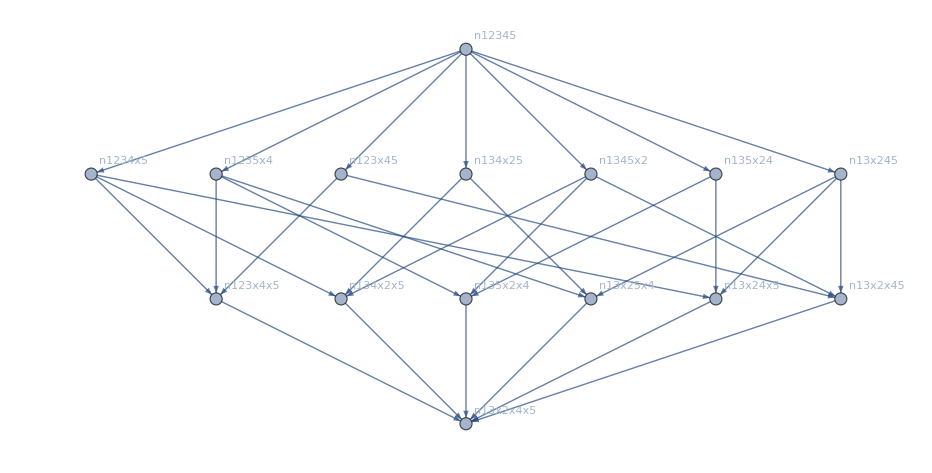

```mathematica
Graph[GraphEndsIn[four,n13x2x4x5],GraphLayout->"LayeredDigraphEmbedding",DirectedEdges->False,VertexLabels->"Name"]
```

```mathematica
allGraphs[quad1Key,"colofourrealnull"]/.simpRep//Hold
```

Hold[allGraphs[quad1Key,colofourrealnull]/.simpRep]

```mathematica
AndToTable[allGraphs[quad1Key,"colofourrealnull"]]
```

{-6 n12345,2 n1234x5,2 n1235x4,n123x45,-n123x4x5,2 n1345x2,n134x25,-n134x2x5,n135x24,-n135x2x4,2 n13x245,-n13x24x5,-n13x25x4,-n13x2x45,n13x2x4x5}

```mathematica
hand=AndToTable[allGraphs[quad1Key,"colofourrealnull"]]
```

{-6 n12345,2 n1234x5,2 n1235x4,n123x45,-n123x4x5,2 n1345x2,n134x25,-n134x2x5,n135x24,-n135x2x4,2 n13x245,-n13x24x5,-n13x25x4,-n13x2x45,n13x2x4x5}

```mathematica
Table[allGraphs[k,"graph"],{k,{quad1Key,quad2Key,quad3Key,quad4Key,quad5Key}}]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
(Map[(#/.simpRep)->#&,AndToTable[allGraphs[quad1Key,"colofourrealnull"]]]//Sort)/.repcolofourrealnullgraph2
```

{-6→-6 -Graphics-n1234559048,λ→-Graphics-n123x4552976,λ→-Graphics-n134x2517568,λ→-Graphics-n135x2414748,2 λ→2 -Graphics-n1234x557528,2 λ→2 -Graphics-n1235x454492,2 λ→2 -Graphics-n1345x218980,2 λ→2 -Graphics-n13x24513340,-λ^2→--Graphics-n123x4x552974,-λ^2→--Graphics-n134x2x517514,-λ^2→--Graphics-n135x2x414586,-λ^2→--Graphics-n13x24x513284,-λ^2→--Graphics-n13x25x413176,-λ^2→--Graphics-n13x2x4513124,λ^3→-Graphics-n13x2x4x513122}

```mathematica
Table[allGraphs[k,"graph"],{k,{alfa1Key,beta1Key,gamma1Key,delta1Key,epsilon1Key}}]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
(Map[(#/.simpRep)->#&,AndToTable[allGraphs[alfa1Key,"colofourrealnull"]]]//Sort)/.repcolofourrealnullgraph2
```

{2→2 -Graphics-n1234559048,-λ→--Graphics-n1234x557528,-λ→--Graphics-n135x2414748,-λ→--Graphics-n13x24513340,λ^2→-Graphics-n13x24x513284}

```mathematica
(Map[(#/.simpRep)->#&,AndToTable[allGraphs[delta1Key,"colofourrealnull"]]]//Sort)/.repcolofourrealnullgraph2
```

{2→2 -Graphics-n1234559048,-λ→--Graphics-n1235x454492,-λ→--Graphics-n134x2517568,-λ→--Graphics-n13x24513340,λ^2→-Graphics-n13x25x413176}

```mathematica
AndToTable[Total[Table[allGraphs[k,"colofourrealnull"],{k,{quad1Key,alfa1Key,delta1Key}}]]]
```

{-2 n12345,n1234x5,n1235x4,n123x45,-n123x4x5,2 n1345x2,-n134x2x5,-n135x2x4,-n13x2x45,n13x2x4x5}

```mathematica
AndToTable[Total[Table[allGraphs[k,"colofourrealnull"],{k,{quad2Key,alfa1Key,gamma1Key}}]]]
```

{-2 n12345,n1234x5,2 n1245x3,-n124x3x5,n15x234,-n15x24x3,n1x2345,-n1x234x5,-n1x245x3,n1x24x3x5}

```mathematica
AndToTable[Total[Table[allGraphs[k,"colofourrealnull"],{k,{quad3Key,gamma1Key,epsilon1Key}}]]]
```

{-2 n12345,2 n1235x4,n12x345,-n12x35x4,n1345x2,-n135x2x4,n1x2345,-n1x235x4,-n1x2x345,n1x2x35x4}

```mathematica
AndToTable[Total[Table[allGraphs[k,"colofourrealnull"],{k,{quad4Key,beta1Key,epsilon1Key}}]]]
```

{-2 n12345,2 n1234x5,n1245x3,-n124x3x5,n1345x2,-n134x2x5,n145x23,-n145x2x3,-n14x23x5,n14x2x3x5}

```mathematica
AndToTable[Total[Table[allGraphs[k,"colofourrealnull"],{k,{quad5Key,beta1Key,delta1Key}}]]]
```

{-2 n12345,n1235x4,n1245x3,n125x34,-n125x3x4,2 n1x2345,-n1x235x4,-n1x245x3,-n1x25x34,n1x25x3x4}

```mathematica
Total[Table[allGraphs[k,"colofourrealnull"],{k,{quad1Key,quad2Key,quad3Key,quad4Key,quad5Key,alfa1Key,beta1Key,gamma1Key,delta1Key,epsilon1Key,alfa1Key,beta1Key,gamma1Key,delta1Key,epsilon1Key}}]]/.simpRep
```

-10+25 λ-20 λ^2+5 λ^3

```mathematica
AndToTable[Total[Table[allGraphs[k,"colofourrealnull"],{k,{quad1Key,alfa1Key,delta1Key}}]]-Total[Table[allGraphs[k,"colofourrealnull"],{k,{quad2Key,alfa1Key,gamma1Key}}]]]
```

{n1235x4,n123x45,-n123x4x5,-2 n1245x3,n124x3x5,2 n1345x2,-n134x2x5,-n135x2x4,-n13x2x45,n13x2x4x5,-n15x234,n15x24x3,-n1x2345,n1x234x5,n1x245x3,-n1x24x3x5}

```mathematica
Solve[-10+25 λ-20 λ^2+5 λ^3==0]
```

{{λ→1},{λ→1},{λ→2}}

```mathematica
Total[Table[allGraphs[k,"colofourrealnull"],{k,{quad5Key,beta1Key,delta1Key}}]]
```

-2 n12345+n1235x4+n1245x3+n125x34-n125x3x4+2 n1x2345-n1x235x4-n1x245x3-n1x25x34+n1x25x3x4

```mathematica
Select[Keys[allGraphs],allGraphs[#,"colofourrealnull"]==-2 n12345+n1235x4+n1245x3+n125x34-n125x3x4+2 n1x2345-n1x235x4-n1x245x3-n1x25x34+n1x25x3x4&]
```

{20803}

```mathematica
Select[Keys[allGraphs],allGraphs[#,"colofourrealnull"]==Total[Table[allGraphs[k,"colofourrealnull"],{k,{quad1Key,alfa1Key}}]]&]
```

{36004}

```mathematica
allGraphs[36004,"colofourrealnull"]/.simpRep
```

-4+8 λ-5 λ^2+λ^3

```mathematica
Total[Table[allGraphs[k,"colofourrealnull"],{k,{alfaKey,betaKey,gammaKey,deltaKey,epsilonKey}}]]/5//Simplify
```

1/5 (-10 n12345+4 n1234x5+4 n1235x4+n123x45-n123x4x5+4 n1245x3-2 n124x3x5+n125x34-n125x3x4+n12x345-n12x35x4+4 n1345x2-2 n134x2x5-2 n135x2x4-n13x2x45+n13x2x4x5+n145x23-n145x2x3-n14x23x5+n14x2x3x5+n15x234-n15x24x3+4 n1x2345-n1x234x5-2 n1x235x4-2 n1x245x3+n1x24x3x5-n1x25x34+n1x25x3x4-n1x2x345+n1x2x35x4)

```mathematica
Table[allGraphs[k,"colofourrealnull"]/.simpRep,{k,{alfaKey,betaKey,gammaKey,deltaKey,epsilonKey}}]
```

{-2+5 λ-4 λ^2+λ^3,-2+5 λ-4 λ^2+λ^3,-2+5 λ-4 λ^2+λ^3,-2+5 λ-4 λ^2+λ^3,-2+5 λ-4 λ^2+λ^3}

```mathematica
ChromaticPolynomial[allGraphs[alfaKey,"graph"],x]/.x->4
```

72

```mathematica
ChromaticPolynomial[allGraphs[quad1Key,"graph"],x]/.x->4
```

24

```mathematica
(Map[(#/.simpRep)->#&,AndToTable[allGraphs[k5Key,"colofourrealnull"]]]//Sort)
```

{24→24 n12345,-6 λ→-6 n1234x5,-6 λ→-6 n1235x4,-6 λ→-6 n1245x3,-6 λ→-6 n1345x2,-6 λ→-6 n1x2345,-2 λ→-2 n123x45,-2 λ→-2 n124x35,-2 λ→-2 n125x34,-2 λ→-2 n12x345,-2 λ→-2 n134x25,-2 λ→-2 n135x24,-2 λ→-2 n13x245,-2 λ→-2 n145x23,-2 λ→-2 n14x235,-2 λ→-2 n15x234,λ^2→n12x34x5,λ^2→n12x35x4,λ^2→n12x3x45,λ^2→n13x24x5,λ^2→n13x25x4,λ^2→n13x2x45,λ^2→n14x23x5,λ^2→n14x25x3,λ^2→n14x2x35,λ^2→n15x23x4,λ^2→n15x24x3,λ^2→n15x2x34,λ^2→n1x23x45,λ^2→n1x24x35,λ^2→n1x25x34,2 λ^2→2 n123x4x5,2 λ^2→2 n124x3x5,2 λ^2→2 n125x3x4,2 λ^2→2 n134x2x5,2 λ^2→2 n135x2x4,2 λ^2→2 n145x2x3,2 λ^2→2 n1x234x5,2 λ^2→2 n1x235x4,2 λ^2→2 n1x245x3,2 λ^2→2 n1x2x345,-λ^3→-n12x3x4x5,-λ^3→-n13x2x4x5,-λ^3→-n14x2x3x5,-λ^3→-n15x2x3x4,-λ^3→-n1x23x4x5,-λ^3→-n1x24x3x5,-λ^3→-n1x25x3x4,-λ^3→-n1x2x34x5,-λ^3→-n1x2x35x4,-λ^3→-n1x2x3x45,λ^4→n1x2x3x4x5}

```mathematica
Table[Labeled[allGraphs[k,"graph"],k],{k,Select[Keys[allGraphs],EdgeCount[allGraphs[#,"graph"]]==9&]}]
```

{-Graphics-29523,-Graphics-29521,-Graphics-29515,-Graphics-29497,-Graphics-29443,-Graphics-29281,-Graphics-28795,-Graphics-27337,-Graphics-22963,-Graphics-9841}

```mathematica
allGraphs[29523,"graph"]
```

-Graphics-

```mathematica
(Map[(#/.simpRep)->#&,AndToTable[allGraphs[29523,"colofourrealnull"]]]//Sort)
```

{18→18 n12345,-6 λ→-6 n1234x5,-6 λ→-6 n1235x4,-4 λ→-4 n1245x3,-4 λ→-4 n1345x2,-4 λ→-4 n1x2345,-2 λ→-2 n124x35,-2 λ→-2 n125x34,-2 λ→-2 n134x25,-2 λ→-2 n135x24,-2 λ→-2 n14x235,-2 λ→-2 n15x234,-λ→-n12x345,-λ→-n13x245,-λ→-n145x23,λ^2→n12x34x5,λ^2→n12x35x4,λ^2→n13x24x5,λ^2→n13x25x4,λ^2→n145x2x3,λ^2→n14x23x5,λ^2→n14x25x3,λ^2→n14x2x35,λ^2→n15x23x4,λ^2→n15x24x3,λ^2→n15x2x34,λ^2→n1x245x3,λ^2→n1x24x35,λ^2→n1x25x34,λ^2→n1x2x345,2 λ^2→2 n123x4x5,2 λ^2→2 n124x3x5,2 λ^2→2 n125x3x4,2 λ^2→2 n134x2x5,2 λ^2→2 n135x2x4,2 λ^2→2 n1x234x5,2 λ^2→2 n1x235x4,-λ^3→-n12x3x4x5,-λ^3→-n13x2x4x5,-λ^3→-n14x2x3x5,-λ^3→-n15x2x3x4,-λ^3→-n1x23x4x5,-λ^3→-n1x24x3x5,-λ^3→-n1x25x3x4,-λ^3→-n1x2x34x5,-λ^3→-n1x2x35x4,λ^4→n1x2x3x4x5}

```mathematica
(Map[(#/.simpRep)->#&,AndToTable[allGraphs[k5Key,"colofourrealnull"]-allGraphs[29523,"colofourrealnull"]]]//Sort)
```

{6→6 n12345,-2 λ→-2 n123x45,-2 λ→-2 n1245x3,-2 λ→-2 n1345x2,-2 λ→-2 n1x2345,-λ→-n12x345,-λ→-n13x245,-λ→-n145x23,λ^2→n12x3x45,λ^2→n13x2x45,λ^2→n145x2x3,λ^2→n1x23x45,λ^2→n1x245x3,λ^2→n1x2x345,-λ^3→-n1x2x3x45}

```mathematica
(allGraphs[k5Key,"colofourrealnull"]-allGraphs[29523,"colofourrealnull"])
```

6 n12345-2 n123x45-2 n1245x3-n12x345+n12x3x45-2 n1345x2-n13x245+n13x2x45-n145x23+n145x2x3-2 n1x2345+n1x23x45+n1x245x3+n1x2x345-n1x2x3x45

```mathematica
(allGraphs[k5Key,"colofourrealnull"]-allGraphs[29523,"colofourrealnull"])/.simpRep
```

6-11 λ+6 λ^2-λ^3

```mathematica
ChromaticPolynomial[CompleteGraph[4],x]/x//Simplify
```

-6+11 x-6 x^2+x^3

```mathematica
Select[Keys[allGraphs],VertexCount[allGraphs[#,"graph"]]==4&&EdgeCount[allGraphs[#,"graph"]]==4&]
```

{29502,29574,29436,29460,29405,29736,29676,29647,29270,29296,29247,29350,29325,29205,29223,29174,29176,29182,30163,30001,29929,28800,28777,28873,28848,29037,29008,28948,28624,28480,31681,31465,31441,30978,30954,30738,27330,27355,27259,27282,27579,27550,27490,27118,27070,28056,27984,27822,26597,26501,26851,26366,36057,36003,35977,35352,35326,35272,33888,33862,33808,33157,22952,22981,23041,23016,22908,22856,22721,22744,22792,23680,23608,23446,22227,22315,22156,21967,25138,25114,24898,24411,20781,20803,20758,20461,21501,20048,20050,20056,49203,49197,49195,48450,48448,48442,46938,46936,46930,46183,42402,42400,42394,41647,40135,9846,9834,9830,9823,9763,9734,9599,9574,9526,10534,10462,10300,9121,9130,9057,8893,11944,11920,11704,11217,7657,7732,7707,7483,8355,6926,6952,7006,16158,16132,16078,15427,13963,3281,3522,3493,3433,3979,2554,2578,2794,5377,1102,1174,1336}

```mathematica
Table[(allGraphs[lambdaKey,"colofourrealnull"]-allGraphs[k,"colofourrealnull"]),{k,Select[Keys[allGraphs],With[{g=allGraphs[#,"graph"]},VertexCount[g]==5&&EdgeQ[g,1<->2]&&EdgeQ[g,2<->3]&&EdgeQ[g,3<->4]&&EdgeQ[g,4<->5]&&EdgeQ[g,5<->1]&&EdgeCount[g]==6]&]}]/.simpRep//Tally//TableForm
```

-2+5 λ-4 λ^2+λ^3 | 5

```mathematica
Table[(allGraphs[k,"colofourrealnull"]-allGraphs[lambdaKey,"colofourrealnull"]),{k,Select[Keys[allGraphs],With[{g=allGraphs[#,"graph"]},VertexCount[g]==5&&EdgeQ[g,1<->2]&&EdgeQ[g,2<->3]&&EdgeQ[g,3<->4]&&EdgeQ[g,4<->5]&&EdgeQ[g,5<->1]&&EdgeCount[g]==10]&]}]/.simpRep//Tally//TableForm
```

20-40 λ+25 λ^2-5 λ^3 | 1

```mathematica
Table[(allGraphs[lambdaKey,"colofourrealnull"]-allGraphs[k,"colofourrealnull"]),{k,Select[Keys[allGraphs],VertexCount[allGraphs[#,"graph"]]==4&&EdgeCount[allGraphs[#,"graph"]]==4&]}]/.simpRep
```

```mathematica
Table[(allGraphs[k5Key,"colofourrealnull"]-allGraphs[k,"colofourrealnull"]),{k,Select[Keys[allGraphs],EdgeCount[allGraphs[#,"graph"]]==9&]}]/.simpRep//TableForm
```

6-11 λ+6 λ^2-λ^3
6-11 λ+6 λ^2-λ^3
6-11 λ+6 λ^2-λ^3
6-11 λ+6 λ^2-λ^3
6-11 λ+6 λ^2-λ^3
6-11 λ+6 λ^2-λ^3
6-11 λ+6 λ^2-λ^3
6-11 λ+6 λ^2-λ^3
6-11 λ+6 λ^2-λ^3
6-11 λ+6 λ^2-λ^3